## NIG factor model stuff

```mathematica
Clear[α,β,μ,δ,μ1,μ2,δ1,δ2]
```

See https://en.wikipedia.org/wiki/Bessel_function: The modified Bessel function of the second kind has also been called [..] Modified Bessel function of the third kind.

```mathematica
q[x_]:=√(1+x^2);
g[x_,α_,β_,μ_,δ_]:=(α Exp[δ √(α^2-β^2)-β μ] BesselK[1,δ α q[(x-μ)/δ]] Exp[β x])/(π q[(x-μ)/δ]);
```

```mathematica
M[u_,α_,β_,μ_,δ_]:=Exp[δ (√(α^2-β^2)-√(α^2-(β+u)^2))+μ u]
```

Expectation

```mathematica
Simplify[D[M[u,α,β,μ,δ], u]/.u->0]
```

(β δ)/(√(α^2-β^2))+μ

```mathematica
ENIG[α_,β_,μ_,δ_]:=μ+(δ β)/(√(α^2-β^2));
```

Variance

```mathematica
Simplify[D[M[u,α,β,μ,δ], {u,2}]-ENIG[α,β,μ,δ]^2/.u->0]
```

(α^2 δ)/((α^2-β^2)^(3/2))

```mathematica
VNIG[α_,β_,μ_,δ_]:=(α^2 δ)/((α^2-β^2)^(3/2));
```

Skewness
(see https://en.wikipedia.org/wiki/Skewness)

```mathematica
Simplify[(D[M[u,α,β,μ,δ], {u,3}]-3 ENIG[α,β,μ,δ] VNIG[α,β,μ,δ]-ENIG[α,β,μ,δ]^3)/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

```mathematica
SNIG[α_,β_,μ_,δ_]:=(3 β)/(α √δ (α^2-β^2)^(1/4))
```

Centering inside the moment generating function:

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,3}]/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0,δ>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,3}]/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0,δ>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

Kurtosis

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,4}]/VNIG[α,β,μ,δ]^2/.u->0,Assumptions->α>0]
```

(3 (α^2+4 β^2))/(α^2 δ √(α^2-β^2))+3

```mathematica
KNIG[α_,β_,μ_,δ_]:=(3 (α^2+4 β^2))/(α^2 δ √(α^2-β^2))+3
```

Simulate  NIG’s

```mathematica
d[x_,α_,β_,δ_]:=(Exp[δ √(α^2-β^2)] x^(-3/2) Exp[-(δ^2/x+(α^2-β^2) x)/2])/(√(2 π))
```

```mathematica
μ=0;
μ1=-1;
μ2=0.5;
δ=0.5;
δ1=2;
δ2=1;
β=-3;
α=8;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
n=100000;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
```

```mathematica
X1 = Z + Z1;
X2 = Z + Z2;
```

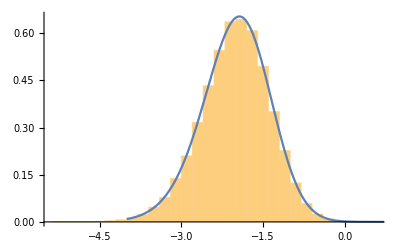
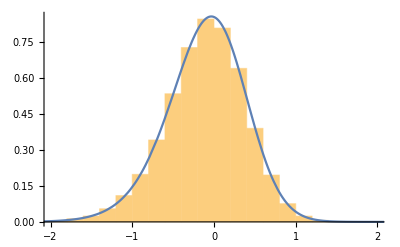

```mathematica
{Show[
Histogram[X1,Automatic, "PDF"],
Plot[g[x,α,β,μ+μ1,δ+δ1], {x,-4,5}]
],
Show[
Histogram[X2,Automatic, "PDF"],
Plot[g[x,α,β,μ+μ2,δ+δ2], {x,-4,5},PlotRange->Full]
]}
```

```mathematica
EX1=ENIG[α, β, μ+μ1,δ+δ1];
EX2=ENIG[α, β,μ+μ2,δ+δ2];
```

```mathematica
VX1=VNIG[α,β,μ+μ1,δ+δ1];
VX2=VNIG[α,β, μ+μ2,δ+δ2];
VZ = VNIG[α,β,μ,δ];
```

```mathematica
N[{{Mean[X1], EX1}, {Variance[X1], VX1}, {Mean[X2],EX2}, {Variance[X2], VX2}}//TableForm]
```

-2.01145 | -2.0113
0.389201 | 0.392262
-0.108986 | -0.10678
0.235726 | 0.235357

Covariance

```mathematica
N[{VZ, Covariance[X1,X2]}]
```

{0.0784523,0.0777727}

Correlation

```mathematica
N[{√(δ^2/((δ+δ1) (δ+δ2))),Correlation[X1,X2]}]
```

{0.258199,0.256766}

```mathematica
N[Table[{Moment[X1,r],D[M[u,α,β,μ+μ1, δ+δ1], {u,r}]/.u->0}, {r,1,10}]//TableForm]
```

-2.01145 | -2.0113
4.43513 | 4.43759
-10.5506 | -10.5674
26.8231 | 26.9025
-72.3974 | -72.7361
206.412 | 207.833
-619.122 | -625.235
1946.91 | 1974.3
-6398.99 | -6527.34
21920.2 | 22547.5

```mathematica
N[Table[{Moment[X2,r],D[M[u,α,β,μ+μ2, δ+δ2], {u,r}]/.u->0}, {r,1,10}]//TableForm]
```

-0.108986 | -0.10678
0.247601 | 0.246759
-0.118438 | -0.115125
0.226431 | 0.222201
-0.224175 | -0.213612
0.429762 | 0.407466
-0.665629 | -0.60406
1.41791 | 1.24808
-2.96102 | -2.44571
7.24709 | 5.69069

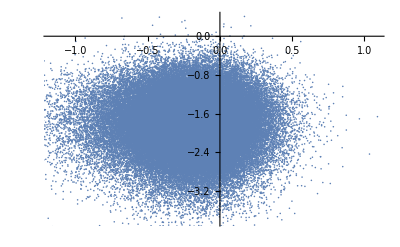
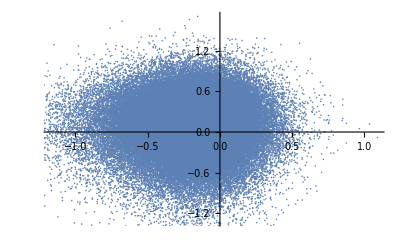

```mathematica
{ListPlot[{Z,Z1}ᵀ], ListPlot[{Z,Z2}ᵀ]}
```

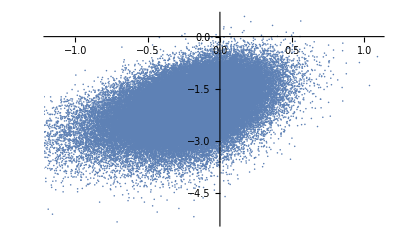
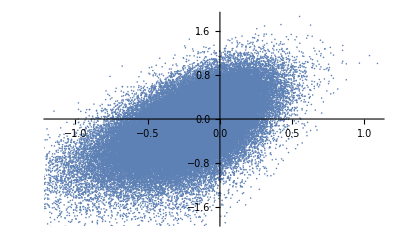

```mathematica
{ListPlot[{Z,X1}ᵀ],ListPlot[{Z,X2}ᵀ]}
```

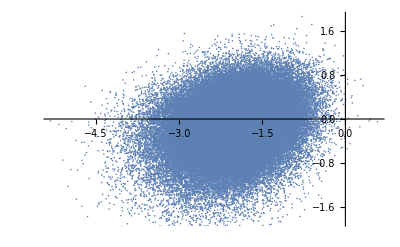

```mathematica
ListPlot[{X1, X2}ᵀ]
```

#### ML estimates of parameters

These work remarkably bad.

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X1[[1;;10]],α,β,μ,δ]]];NMaximize[{LL[α0,5,-1,3],α0>5}, α0]
```

{-119.588,{α0→13.917}}

```mathematica
{LL[α,β,μ+μ1,δ+δ1],{α,β,μ+μ1,δ+δ1}}
```

{-10.1055,{8,-3,-1,2.5}}

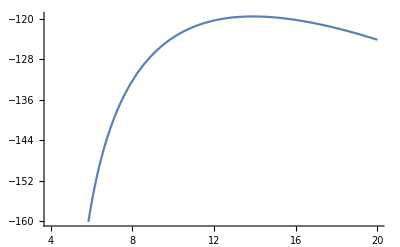

```mathematica
Plot[LL[α0, 5, -1, 3], {α0,4,20}]
```

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X1[[1;;10]],α,β,μ,δ]]];NMaximize[{LL[α0,β0,μ0,δ0],α0>2 && Abs[β0]<α0,δ0>0}, {α0,β0,μ0,δ0}]
{LL[α,β,μ+μ1,δ+δ1],{α,β,μ+μ1,δ+δ1}}
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-9.89919,{α0→106.521,β0→-103.255,μ0→0.756471,δ0→0.720769}}

{-10.1055,{8,-3,-1,2.5}}

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X2[[1;;10]],α,β,μ,δ]]];NMaximize[{LL[α0,β0,μ0,δ0],α0>2 && Abs[β0]<α0,δ0>0}, {α0,β0,μ0,δ0}]
{LL[α,β,μ+μ2,δ+δ2],{α,β,μ+μ2,δ+δ2}}
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-4.88033,{α0→25.6002,β0→-18.2086,μ0→1.69948,δ0→1.49614}}

{-6.99334,{8,-3,0.5,1.5}}

#### Method of moments

This performs much better

```mathematica
e1=Table[(Moment[X1,r]-D[M[u,α0,β0,μ10,δ10],{u,r}]/.u->0)==0, {r,1,4}];
sol1=NSolve[Flatten[{e1 ,δ10>0,α0>3, Abs[β0]<α0}], {α0,β0,μ10,δ10}]
{α,β,μ+μ1, δ+δ1}
```

{{α0→8.27752,μ10→-0.954322,δ10→2.53128,β0→-3.1899}}

{8,-3,-1,2.5}

```mathematica
e2=Table[(Moment[X2,r]-D[M[u,α0,β0,μ20,δ20],{u,r}]/.u->0)==0, {r,1,4}];
sol2=NSolve[Flatten[{e2 ,δ20>0,α0>3, Abs[β0]<α0}], {α0,β0,μ20,δ20}]
{α,β,μ+μ2, δ+δ2}
```

{{α0→7.67072,μ20→0.472567,δ20→1.44258,β0→-2.86804}}

{8,-3,0.5,1.5}

```mathematica
e1=Table[(Moment[X1,r]-D[M[u,α0,β0,μ10,δ10],{u,r}]/.u->0), {r,1,4}];
e2=Table[(Moment[X2,r]-D[M[u,α0,β0,μ20,δ20],{u,r}]/.u->0), {r,1,4}];
```

```mathematica
e=RootMeanSquare[Flatten[Join[e1,e2]]];
cons={δ10>0,δ20>0,α0>Min[α0/.sol1⟦1⟧,α0/.sol2⟦1⟧],α0<Max[α0/.sol1⟦1⟧,α0/.sol2⟦1⟧],Abs[β0]<α0};
sol=NMinimize[{e,cons},{α0,β0,μ10,δ10,μ20,δ20}]
```

{0.000296772,{α0→7.67432,β0→-2.84802,μ10→-1.05917,δ10→2.38385,μ20→0.470211,δ20→1.44964}}

```mathematica
{α,β,μ1, δ1, μ2, δ2}
```

{8,-3,-1,2,0.5,1}

```mathematica
sol3=NSolve[Correlation[X1,X2]==δ0/(√((δ0+δ10/.sol⟦2⟧) (δ0+δ20/.sol⟦2⟧))),δ0]
```

{{δ0→0.647356}}

```mathematica
{Correlation[X1,X2],δ0/(√((δ0+δ10/.sol⟦2⟧) (δ0+δ20/.sol⟦2⟧)))/.sol3⟦1⟧,δ/(√((δ+δ1) (δ+δ2)))}
```

{0.256766,0.256766,0.258199}

WLOG set μ to zero.

### Modules

```mathematica
FitNIG[data_]:=Module[{e,α,β,μ,δ,sol1},
e=Table[(Moment[data,r]-D[M[u,α,β,μ,δ],{u,r}]/.u->0)==0, {r,1,4}];
sol1=NSolve[Flatten[{e ,δ>0,α>3, Abs[β]<α}], {α,β,μ,δ}];
{α,β,μ,δ}/.sol1[[1]]
]
```

```mathematica
FitJointNIG[d1_,d2_,αlb_,αub_]:=Module[{e1,e2,α,β,μ1,μ2,δ1,δ2,e,cons,sol},
e1=Table[(Moment[d1,r]-D[M[u,α,β,μ1,δ1],{u,r}]/.u->0), {r,1,4}];
e2=Table[(Moment[d2,r]-D[M[u,α,β,μ2,δ2],{u,r}]/.u->0), {r,1,4}];
e=RootMeanSquare[Flatten[Join[e1,e2]]];cons={δ1>0,δ2>0,αlb<α<αub,Abs[β]<α};sol=NMinimize[{e,cons},{α,β,μ1,δ1,μ2,δ2}];
{α,β,μ1,δ1,μ2,δ2}/.sol⟦2⟧
]
```

```mathematica
FitCorrelation[data1_,data2_,δ1_,δ2_]:=Module[{δ,sol3},
sol3=NSolve[Correlation[data1,data2]==δ/(√((δ1) (δ2))),δ];
δ/.sol3⟦1⟧
]
```

### Read BTC data

```mathematica
data=Import[NotebookDirectory[]<> "../processed_data/btc_future_crix.csv"];
```

```mathematica
Dimensions[data]
```

{646,14}

```mathematica
data[[1;;10,12;;13]]
```

(return_btc | return_brr
-0.0226425 | -0.0564519
-0.0667516 | -0.0409618
-0.0522745 | -0.0463652
0.020076 | 0.0120735
0.0174733 | 0.0233977
0.0252517 | 0.0109912
-0.0252517 | -0.012727
0.016472 | 0.00609231
-0.0427781 | -0.0313833)

```mathematica
rbtc=data[[2;;,12]];
rbrr=data[[2;;,13]];
```

```mathematica
Correlation[rbrr,rbtc]
```

0.788286

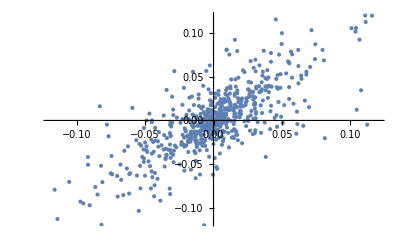

```mathematica
ListPlot[{rbrr,rbtc}ᵀ]
```

```mathematica
{α1,β1,μ1,δ1}=FitNIG[rbrr]
```

{20.1791,-1.11329,0.00228454,0.0350148}

```mathematica
{α2,β2,μ2,δ2}=FitNIG[rbtc]
```

{16.4365,-1.04596,0.00258213,0.0349328}

```mathematica
{α,β,μ1, δ1, μ2, δ2}=FitJointNIG[rbrr,rbtc,Min[α1,α2],Max[α1,α2]]
```

{17.6612,-1.06607,0.00220125,0.030616,0.00262596,0.0375604}

```mathematica
δ=FitCorrelation[rbrr,rbtc,δ1, δ2]
```

0.0267315

Make delta’s incremental

```mathematica
δ1=δ1-δ;
δ2=δ2-δ;
```

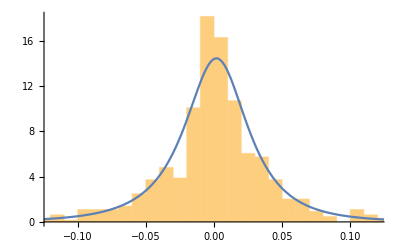
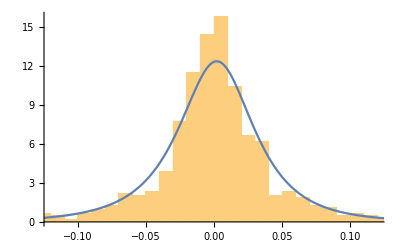

```mathematica
{Show[
Histogram[rbrr, Automatic, "PDF"],
Plot[g[x,α,β,μ1,δ+δ1], {x,-0.3,0.3},PlotRange->All]
],
Show[Histogram[rbtc, Automatic, "PDF"],
Plot[g[x,α,β,μ2,δ+δ2], {x,-0.3, 0.3}, PlotRange->All]
]
}
```

#### Hedge

Z + Z_1-h (Z+Z_2)=(1-h)Z + Z_1-h Z_2

```mathematica
{δ, δ1, δ2}
```

{0.0267315,0.00388452,0.0108289}

```mathematica
γ=√(α^2-β^2);
h=0.95;
x=0.01;
Timing[NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{4.05879,0.733644}

Approximate distribution of hedged position by NIG (it’s not exactly NIG because of the scaling with h, but close as h is close to 1). Match moments.

```mathematica
g1 = M[u,αh, βh, μh, δh]
```

ⅇ^(δh (√(αh^2-βh^2)-√(αh^2-(βh+u)^2))+μh u)

```mathematica
g2=(*M[u,α/(1-h),β/(1-h),0,δ (1-h)]*) M[u,α,β,μ1,δ1] M[-u,α/h,β/h,h μ2,h δ2]
```

exp(0.0102875 (18.5569-√(345.616-(-u-1.12217)^2))+0.00388452 (17.629-√(311.918-(u-1.06607)^2))-0.000293415 u)

```mathematica
{D[g2, {u,1}]/.{u->0},ENIG[αh,βh,μh,δh]/.sol⟦1⟧}
```

{0.0000937855,0.000389453}

```mathematica
{D[g2, {u,2}]/.{u->0},VNIG[αh,βh,μh,δh]+ENIG[αh,βh,μh,δh]^2/.sol⟦1⟧,VNIG[αh,βh,-(βh δh)/(√(αh^2-βh^2)),δh]/.sol⟦1⟧}
```

{0.000777565,0.000615874,0.000615722}

```mathematica
sol=NSolve[Flatten[Join[Table[D[g1,{u,r}]==D[g2,{u,r}]/.{u->0}, {r,1,4}],{αh>0,δh>0}]],{αh,βh,μh,δh}]
```

{{αh→18.1462,μh→-0.000253046,δh→0.0140969,βh→0.446323}}

```mathematica
{α,β,μ1+(1-h)μ2,δ}
```

{17.6612,-1.06607,0.00233255,0.0267315}

```mathematica
Dynamic[x]
```

```mathematica
Timing[t1=Table[NIntegrate[g[y,αh,βh,μh,δh]/.sol[[1]], {y,-∞,x}], {x,-0.1, 0.1,0.01}]]
```

{0.217823,{0.00566739,0.00777025,0.0107957,0.0152466,0.0219827,0.0325595,0.0500046,0.0807822,0.140219,0.265848,0.502963,0.736208,0.858665,0.91729,0.948077,0.965755,0.976601,0.983585,0.988249,0.991451,0.993699}}

```mathematica
γ=√(α^2-β^2);
Timing[t2=Table[NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}],{x,-0.1, 0.1,0.01}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

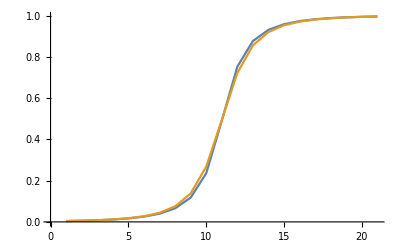

```mathematica
ListPlot[{t1,t2},Joined->True]
```